```mathematica
TH1M=THiggs1Mod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TH2M=THiggs2Mod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TH2P=THiggs2Phase/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TSM=TSingletMod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TSP=TSingletPhase/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TL1M=TLeft1Mod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TL2M=TLeft2Mod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
TL3M=TLeft3Mod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};TR3M=TRight3Mod/.{σn[3]->0,σν[i_]->0}/.{phi2+phiS->alpha,phi2-2phiS->beta};
```

```mathematica
LH1M=Higgs1Mod/.{σn[3]->0,σν[i_]->0}/.{Ybtm->mbottom/v1,Ytop->mtop/v2};
LH2M=Higgs2Mod/.{σn[3]->0,σν[i_]->0}/.{Ybtm->mbottom/v1,Ytop->mtop/v2};
LH2P=Higgs2Phase/.{σn[3]->0,σν[i_]->0}/.{Ybtm->mbottom/v1,Ytop->mtop/v2};
LSM=SingletMod/.{σn[3]->0,σν[i_]->0}/.{Ybtm->mbottom/v1,Ytop->mtop/v2};
LSP=SingletPhase/.{σn[3]->0,σν[i_]->0}/.{Ybtm->mbottom/v1,Ytop->mtop/v2};
LL1M=Left1Mod/.{σn[3]->0,σν[i_]->0};
LL2M=Left2Mod/.{σn[3]->0,σν[i_]->0};
LL3M=Left3Mod/.{σn[3]->0,σν[i_]->0};LR3M=Right3Mod/.{σn[3]->0,σν[i_]->0};
```

```mathematica
Vac3=Flatten[{Solve[TH1M==0,mH1][[1]],
Solve[TH2M==0,mH2][[1]],
Solve[TSM==0,MS][[1]],
{σn[3]->0,σν[i_]->0}}];
```

```mathematica
Vac3L=Flatten[{Solve[LH1M==0,mH1][[1]],
Solve[LH2M==0,mH2][[1]],
Solve[LSM==0,MS][[1]],
Solve[LH2P==0,A0][[1]],
Solve[LSP==0,A3][[1]],
{σn[3]->0,σν[i_]->0}}];
```

```mathematica
TE3=Mneut[[Range[1,3],Range[1,3]]]/.Vac3L;
TO3=Mneut[[Range[4,6],Range[4,6]]]/.Vac3L;
TC3=Mchar/.Vac3L;
```

```mathematica
LE3=Mne1l[[Range[1,3],Range[1,3]]]/.{σn[3]->0,σν[i_]->0}/.{MD33^2->MQ33^2,MU33^2->MQ33^2};
LO3=Mne1l[[Range[4,6],Range[4,6]]]/.{σn[3]->0,σν[i_]->0}/.{MD33^2->MQ33^2,MU33^2->MQ33^2};
LC3=Mch1l/.{σn[3]->0,σν[i_]->0}/.{MD33^2->MQ33^2,MU33^2->MQ33^2};
```

```mathematica
TN6=Mneut//.Vac3L;
LN6=Mne1l/.{σn[3]->0,σν[i_]->0}/.{MD33^2->MQ33^2,MU33^2->MQ33^2}//.Vac3L;
TC3=Mchar//.Vac3L;
LC3=Mch1l/.{σn[3]->0,σν[i_]->0}/.{MD33^2->MQ33^2,MU33^2->MQ33^2}//.Vac3L;
```

```mathematica
MslN=MslepN//.Vac3L//Simplify;
MslC=MslepC//.Vac3L//Simplify;
```

```mathematica
Mcχ=Mchχ//.Vac3L//Simplify;
McχT=MchχT//.Vac3L//Simplify;
Mnχ=Mneχ//.Vac3L//Simplify;
```

```mathematica
prec=50;
$MinPrecision=prec;
TeV=10^12;GeV=10^9;MeV=10^6;
vSq=SetPrecision[(174GeV)^2,prec];
vSqHiggs = (vSq - σν[1]^2- σν[2]^2- σν[3]^2)/.{σn[3]->0,σν[i_]->0};
mW=SetPrecision[80.403GeV,prec];
mZ=SetPrecision[91.1876GeV,prec];
αew=SetPrecision[1/127.908957,prec];θw=SetPrecision[ArcSin[Sqrt[0.23124]],prec];mtPole=SetPrecision[180GeV,prec];
αstrong=SetPrecision[0.102,prec];
mup=SetPrecision[1.5MeV,prec];
mcharm=SetPrecision[1.1GeV,prec];mtop=SetPrecision[mtPole/(1+4*αstrong/(3 Pi)),prec];
mdown=SetPrecision[3MeV,prec];
mstrange=SetPrecision[60MeV,prec];
mbottom=SetPrecision[4.1GeV,prec];
melectron=SetPrecision[0.511MeV,prec];
mmuon=SetPrecision[105.66MeV,prec];
mtau=SetPrecision[1.777GeV,prec];
(*Yup=SetPrecision[mup /v2,prec];
Ycrm=SetPrecision[mcharm /v2,prec];*)
Ytop=SetPrecision[mtop /v2,prec];
(*Ydwn=SetPrecision[mdown /v1,prec];
Ystg=SetPrecision[mstrange /v1,prec];*)
Ybtm=SetPrecision[mbottom /v1,prec];
(*Yϵ=SetPrecision[melectron /v1,prec];
Yμ=SetPrecision[mmuon /v1,prec];*)
Ytau=SetPrecision[mtau /v1,prec];
```

```mathematica
β = SetPrecision[ArcTan[10], prec];
g1 := SetPrecision[Sqrt[(2*Tan[θw]^2*mW^2)/vSq], prec];
g2 := SetPrecision[mW*Sqrt[2/vSq], prec];
v1 = Sqrt[vSqHiggs/(1 + Tan[β]^2)];
v2 = v1*Tan[β];
```

```mathematica
varA=Union[Variables[TE3/.{Log[k__]->k}],Variables[TO3/.{Log[k__]->k}],Variables[LE3/.{Log[k__]->k}],Variables[LO3/.{Log[k__]->k}]]
```

```mathematica
varAcp=Union[Variables[TN6/.{Log[k__]->k}/.{Csc[k__]->k,Cot[k__]->k,Cos[k__]->k,Sin[k__]->k}],Variables[LN6/.{Log[k__]->k}/.{Csc[k__]->k,Cot[k__]->k,Cos[k__]->k,Sin[k__]->k}]]
```

{Abtm,Atop,kappa0,kappa3,MD33,MQ33,MU33,phi2,phiS,Rsc,vevS}

```mathematica
varB=Union[Variables[TC3/.{Log[k__]->k}],Variables[LC3/.{Log[k__]->k}]]
```

{A0,Abtm,Atop,kappa0,kappa3,MD33,MQ33,MU33,Rsc,vevS}

```mathematica
varBcp=Union[Variables[TC3/.{Log[k__]->k}/.{Csc[k__]->k,Cot[k__]->k,Cos[k__]->k,Sin[k__]->k}],Variables[LC3/.{Log[k__]->k}/.{Csc[k__]->k,Cot[k__]->k,Cos[k__]->k,Sin[k__]->k}]]
```

{Abtm,Atop,kappa0,kappa3,MD33,MQ33,MU33,phi2,phiS,Rsc,vevS}

```mathematica
varC=Union[Variables[Mcχ/.{Csc[k__]->k,Cot[k__]->k,Cos[k__]->k,Sin[k__]->k}],Variables[Mnχ/.{Csc[k__]->k,Cot[k__]->k,Cos[k__]->k,Sin[k__]->k}]]
```

{kappa0,kappa11,kappa12,kappa13,kappa2,kappa3,M1,M2,phi2,phiS,vevS}

```mathematica
Union[varAcp,varBcp,varC]
```

{Abtm,Atop,kappa0,kappa11,kappa12,kappa13,kappa2,kappa3,M1,M2,MD33,MQ33,MU33,phi2,phiS,Rsc,vevS}

```mathematica
Clear[A1,A2,Abtm,Atop,Atau,kappa0,kappa11,kappa12,kappa13,kappa2,kappa3,M1,M2,MD33,MQ33,MU33,ME33,MN33,ML11,ML22,ML33,phi2,phiS,Rsc,vevS];
```

```mathematica
tt=Table[0,{i,1,50}];
Block[{A1,A2,Abtm,Atop,Atau,kappa0,kappa11,kappa12,kappa13,kappa2,kappa3,M1,M2,MD33,MQ33,MU33,ME33,MN33,ML11,ML22,ML33,phi2,phiS,Rsc,vevS},
For[i=0;x=0,i<50,
x=(34.9+i/250)/50;
$MinPrecision=prec;
(*A0=SetPrecision[TeV,prec];*)
A1[i_]:=SetPrecision[TeV,prec];
A2=SetPrecision[TeV,prec];
(*A3=-SetPrecision[300GeV,prec];*)
Atop=SetPrecision[TeV,prec];
Abtm=SetPrecision[TeV,prec];
Atau=SetPrecision[TeV,prec];
kappa0=SetPrecision[0.4, prec];
kappa11:=SetPrecision[10^-6,prec];
kappa12:=SetPrecision[10^-6,prec];
kappa13:=SetPrecision[10^-6,prec];
kappa2=SetPrecision[0.5,prec];
kappa3=-SetPrecision[0.3,prec];
M1=SetPrecision[350GeV,prec];
M2=SetPrecision[500GeV,prec];
phi2=SetPrecision[2Pi/5,prec];
phiS=SetPrecision[x Pi,prec];
vevS=SetPrecision[TeV,prec];
MD33=MQ33=MU33=SetPrecision[TeV,prec];
ME33=SetPrecision[TeV,prec];
ME11=ME22=ME12=ME13=ME23=SetPrecision[0,prec];
MN33=SetPrecision[TeV,prec];
MN11=MN22=MN12=MN13=MN23=SetPrecision[0,prec];
ML11=ML22=ML33=SetPrecision[TeV,prec];
ML12=ML13=ML23=SetPrecision[0GeV,prec];
Rsc=SetPrecision[500GeV,prec];
(*{valNscE,vecNscE} = Eigensystem[TE3+LE3];
{valNscO,vecNscO} = Eigensystem[TO3+LO3];*)
{valNsc,vecNsc}=Eigensystem[TN6+LN6];
(*{valCsc,vecCsc} = Eigensystem[TC3+LC3];
valN=Sqrt[Eigenvalues[Mnχ.Transpose[Conjugate[Mnχ]]]];
vecN=Inverse[Transpose[Eigenvectors[Mnχ.Transpose[Conjugate[Mnχ]]]]];
valC=Sqrt[Eigenvalues[Conjugate[McχT].Mcχ]];
vecCU=Conjugate[Inverse[Transpose[Eigenvectors[Mcχ.Conjugate[McχT]]]]];
vecCV=Inverse[Transpose[Eigenvectors[Conjugate[McχT].Mcχ]]];
{valNsl,vecNsl}=Eigensystem[Chop[MslepN]];
{valCsl,vecCsl}=Eigensystem[Chop[MslepC]];
mHiggsN=Chop[Sqrt[valSN]];vHiggsN=Chop[vecSN];
mHiggsC=Chop[Sqrt[valSC]];vHiggsC=Chop[vecSC];
mNeutral=Chop[Sqrt[valNsl]];vNeutral=Chop[Inverse[Transpose[vecNsl]]];
mCharged=Chop[Sqrt[valCsl]];vCharged=Chop[Inverse[Transpose[vecCsl]]];
mCharginos=Chop[valC];{vecCU,vecCV}=Chop[{vecCU,vecCV}];
mNeutralinos=Chop[valN];vecN=Chop[vecN];*)
$MinPrecision=0;
i++;
tt[[i]]=N[Chop[valNsc],5];
]
]
```

```mathematica
tt[[2]]
```

{3.8824×10^23,3.7079×10^23,3.396×10^23,1.7077×10^22,-6.6358×10^21,0}

```mathematica
what happens at i =36
```

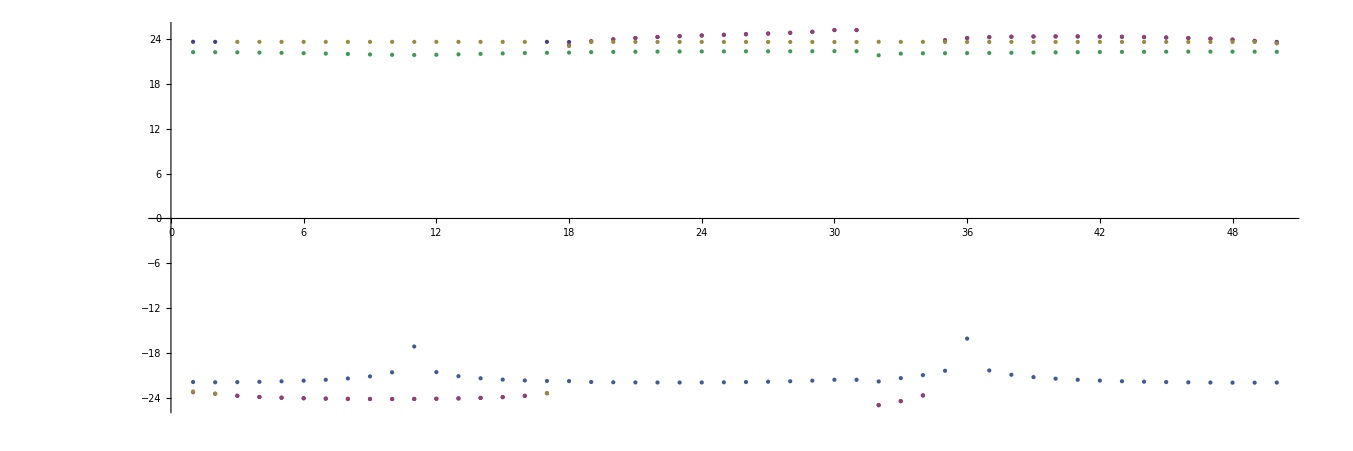

```mathematica
ListPlot[Transpose[Sign[tt]Log[10,Abs[tt]]],AspectRatio->1/3]
```

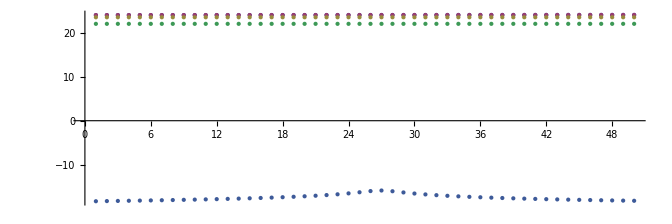

```mathematica
ListPlot[Transpose[Sign[tt]Log[10,Abs[tt]]],AspectRatio->1/3]
```

```mathematica
§
```

```mathematica
ListPlot[Transpose[tt],AspectRatio->1/6,PlotRange->All]
```

```mathematica
Chop[N[vecSNe^2,2],0.01]//MatrixForm
```

```mathematica
N[Sqrt[valSNe]*10^-9,4]//Chop
```

{3380.,250.,120.}

```mathematica
Chop[N[vecSNo^2,2],0.01]//MatrixForm
```

(1. | 0 | 0
0 | 0 | 1.
0 | 1. | 0)

```mathematica
N[Sqrt[valSNo]*10^-9,4]//Chop
```

{3380.,950.,0}

```mathematica
Chop[N[vecSC^2,2],0.01]//MatrixForm
```

(1. | 0
0 | 1.)

```mathematica
N[Sqrt[valSC]*10^-9,4]//Chop
```

{3380.,0}

```mathematica
N[valFC*10^-9,4]//Chop
```

{447.1+37. ⅈ,447.1-37. ⅈ,1.78,0,0}

```mathematica
N[valFN*10^-9,4]//Chop
```

{616.,523.,500.,408.,386.,333.,1.8×10^-10,0,0}

```mathematica
compSe=Transpose[vecSNe^2][[3]];
compSo=Transpose[vecSNo^2][[3]];
compNe=Transpose[vecSNe^2][[7]];
compNo=Transpose[vecSNo^2][[7]];
```

```mathematica
indexSe=If[Max[compSe]>0.95,Position[compSe,Max[compSe]][[1,1]],-99];
indexSo=If[Max[compSo]>0.95,Position[compSo,Max[compSo]][[1,1]],-99];
indexNe=If[Max[compNe]>0.95,Position[compNe,Max[compNe]][[1,1]],-99];
indexNo=If[Max[compNo]>0.95,Position[compNo,Max[compNo]][[1,1]],-99];
```

```mathematica
massSe=If[indexSe≠-99,Sqrt[valSNe][[indexSe]]*10^-9,Infinity];
massSo=If[indexSo≠-99,Sqrt[valSNo][[indexSo]]*10^-9,Infinity];
massNe=If[indexNe≠-99,Sqrt[valSNe][[indexNe]]*10^-9,Infinity];
massNo=If[indexNo≠-99,Sqrt[valSNo][[indexNo]]*10^-9,Infinity];
```

```mathematica
lightestSinglet=Min[{massSe,massSo,massNe,massNo}];
lightestNeutralino=valFN[[6]]*10^-9;
lightestChargino=valFC[[2]]*10^-9;
lightestScalar=Min[{Sqrt[valSNo][[6]]*10^-9,Sqrt[valSNe]*10^-9}];
neutrinoMassEV=valFN[[7]];
canditates=Count[Negative[{massSe,massSo,massNe,massNo}-lightestNeutralino],True];
```

```mathematica
lightestSinglet<lightestNeutralino<lightestChargino
```

True

```mathematica
neutrinoMassEV
```

0.17985742574250956003855312957629743341431499748383

```mathematica
lightestScalar
```

86.24668125042914103003682373505319542591761134142

```mathematica
canditates
```

1

```mathematica
reducedZZH[k_]:=(vecSNe[[k,1]]Cos[β]+vecSNe[[k,2]]Sin[β])^2;
reducedZHH[j_,k_]:=Sqrt[vecSNo[[j,1]]^2+vecSNo[[j,2]]^2](vecSNe[[k,2]]Cos[β]-vecSNe[[k,1]]Sin[β])-Sqrt[vecSNo[[k,1]]^2+vecSNo[[k,2]]^2](vecSNe[[j,2]]Cos[β]-vecSNe[[j,1]]Sin[β]);
```

```mathematica
N[reducedZZH[{1,2,3,4,5,6,7}],4]
```

{6.89×10^-9,0,0,0,0,0.00411,0.996}

```mathematica
tableZHH=Chop[Table[reducedZHH[i,j],{i,1,7},{j,1,7}]];
zerosPositionZHH=Position[tableZHH,0];
zerosNumberZHH=Count[zerosPositionZHH,{_,_}];
mask=Table[1,{i,1,7},{j,1,7}]-Normal[SparseArray[zerosPositionZHH->Table[1,{i,1,zerosNumberZHH}]]];
massSumEvenOdd=Table[Sqrt[valSNe[[i]]]*10^-9+Sqrt[valSNo[[j]]]*10^-9,{i,1,7},{j,1,7}];
```

```mathematica
N[mask*massSumEvenOdd,4]//MatrixForm
```

(0 | 0 | 0 | 0 | 4040. | 3560. | 3360.
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
4230. | 0 | 0 | 0 | 0 | 1060. | 864.
3820. | 0 | 0 | 0 | 1130. | 0 | 458.
3450. | 0 | 0 | 0 | 759. | 283. | 0)